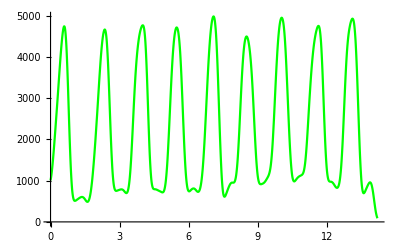

```mathematica
ScaleFactor=50;
FilterForce=Transpose[{ForceData[[;;,1]], ScaleFactor LowpassFilter[ForceData[[;;,2]],1.]}];
FForce=  Interpolation[FilterForce];
ScaleForce=Plot[{FForce [t]},{t,0,14.2},PlotStyle->Green]
```

```mathematica
LT= Range[-8000,8000,2000];
RT= Range[-8000,8000,2000]/ScaleFactor;
FT=Partition[Riffle[LT,RT],2]
```

{{-8000,-160},{-6000,-120},{-4000,-80},{-2000,-40},{0,0},{2000,40},{4000,80},{6000,120},{8000,160}}

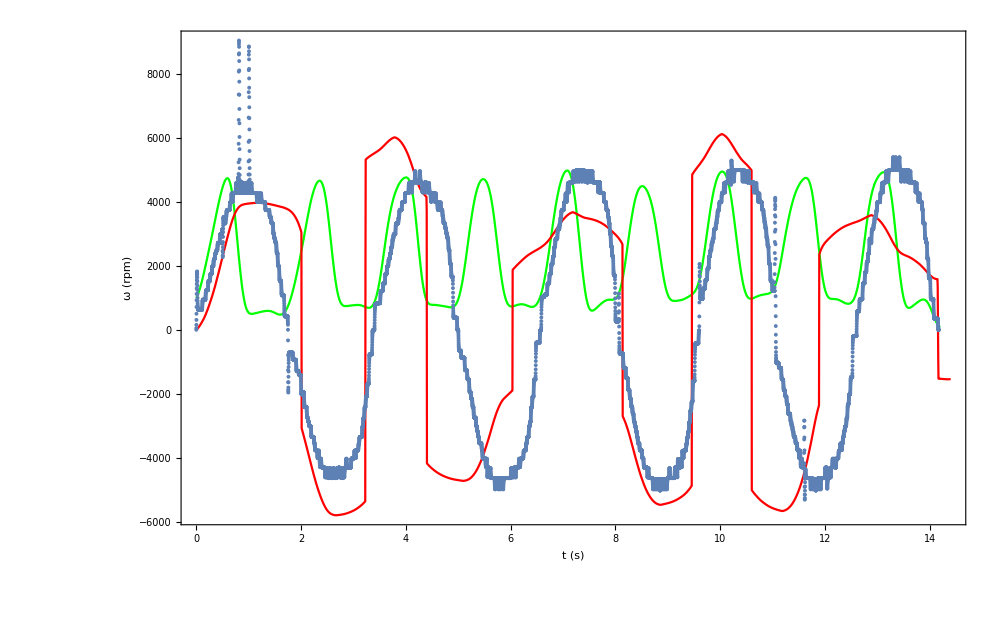

```mathematica
Show[ScaleForce,StudyStringDiameter,Mesu,PlotRange->All,
Frame->True
,Axes->None
,FrameLabel->{{"ω (rpm)","F (N)"},{"t (s)",None}}
,FrameTicks->{{Automatic,FT},{Automatic,Automatic}}
,FrameTicksStyle->{{Blue,Green},{Automatic,Automatic}}
,BaseStyle->{FontSize->20,FontFamily->"Times New Roman"}
,RotateLabel->False
]
```

```mathematica
J ω^2== 2 F (1.4 L^2 Subscript[ρ, s]^2)/((L^2-(Subscript[r, d]+Subscript[r, h])^2)^(3/2))
```

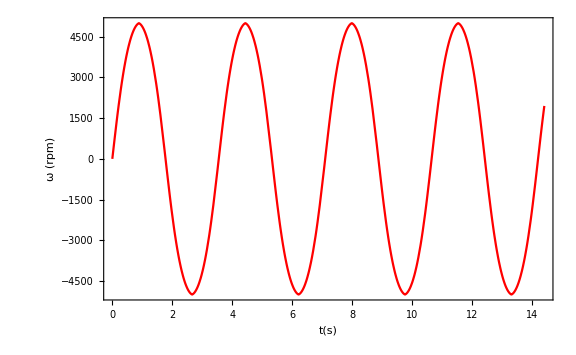
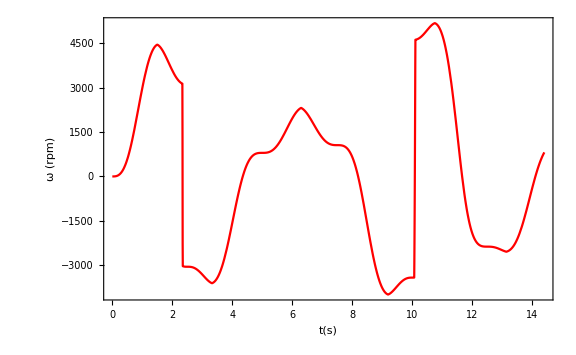
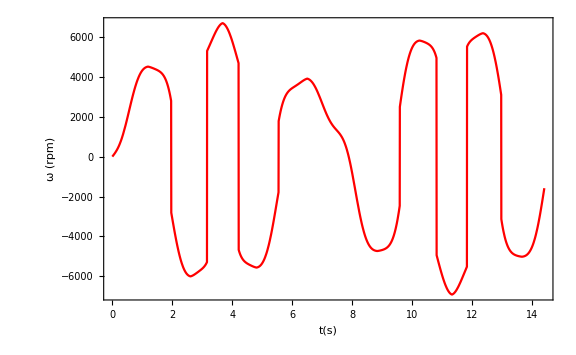
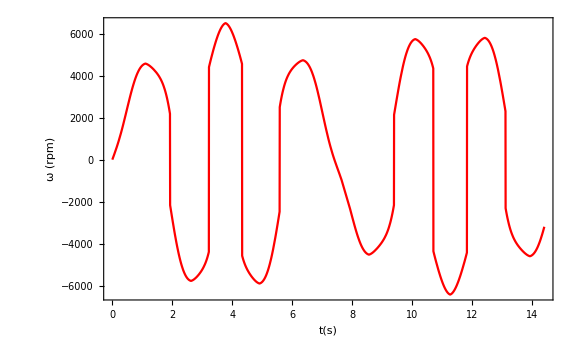
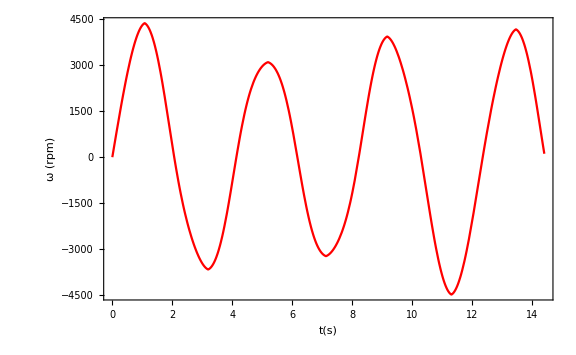
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PredictOmega/@{-100&,-100 Sin[(2π #)/5]^2&,-80 Sin[(2π #)/3]^2-20&,-60 Sin[(2π #)/3]^2-40&,-40 Sin[(2π #)/5]^2-60&,-20-80&}
```

```mathematica
Range[0.0004,0.0006,0.00005]
```

{0.0004,0.00045,0.0005,0.00055,0.0006}

Pattern::patvar: First element in pattern Pattern[0.0004,_] is not a valid pattern name.

Pattern::patvar: First element in pattern Pattern[0.00045,_] is not a valid pattern name.

Pattern::patvar: First element in pattern Pattern[0.0005,_] is not a valid pattern name.

General::stop: Further output of Pattern::patvar will be suppressed during this calculation.

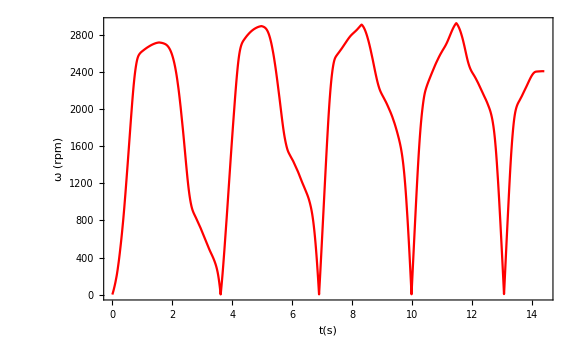
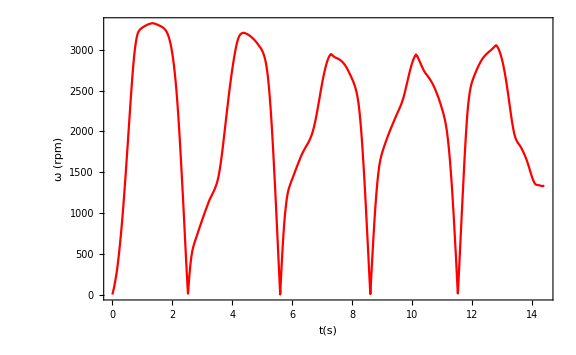
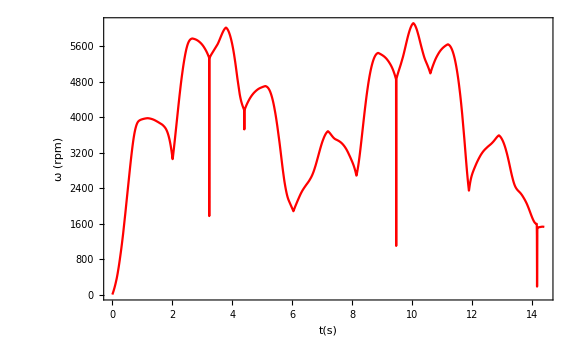
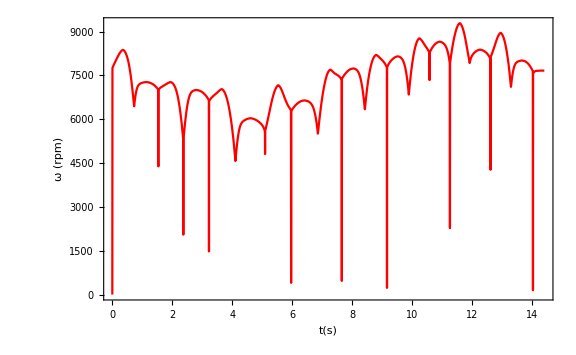
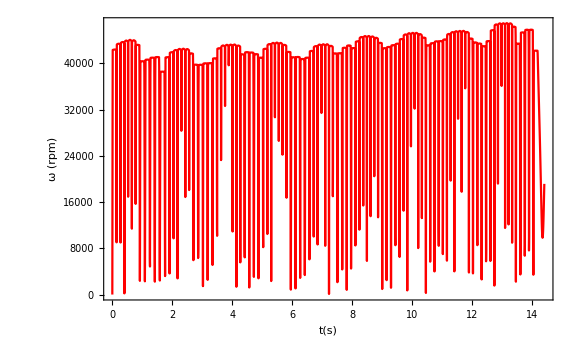

```mathematica
StudyStringDiameter/@Range[0.0004,0.0006,0.00005]
```